# Multiple Linear Regression - Predicting Body Fat

## Mathematica for Research

## Introduction

As an accurate measurement of body fat is costly and it is desirable to have an easy solution for estimating body fat. The dataset contains estimates of the percentage of body fat determined by various body circumference measurements ,  underwater weight and age for 252 men. The algorithm used here will be multiple linear regression with least square estimator.

## Familiarising Dataset

The dataset consist of 252 rows which is the estimate of body fat for 252 men by taking account of  various body circumference measurements and underwater weight. In total there will be 15 columns where body fat will be our target variable and others are predictor variable.

### Variables

The variables in the dataset are list below:

Body Fat (Target variable)			Calculated percent body fat

Density                                                                                 Determined from underwater weighing

Age (years)

Weight (lbs)

Height (inches)

Neck circumference (cm)

Chest circumference (cm)

Abdomen 2 circumference (cm)

Hip circumference (cm)

Thigh circumference (cm)

Knee circumference (cm)

Ankle circumference (cm)

Biceps (extended) circumference (cm)

Forearm circumference (cm)

Wrist circumference (cm)

## Data Import & Wrangling

### Reading dataset

```mathematica
bodyFatData=Import[SystemDialogInput["FileOpen"],{"CSV","Dataset"},"HeaderLines"->1]
```

Dataset[<>]

```mathematica
predictorVariables = {"Density","Age", "Weight", "Height", "Neck", "Chest", "Abdomen", "Hip", "Thigh", "Knee", "Ankle", "Biceps", "Forearm", "Wrist"};
```

```mathematica
bodyFatDataX = bodyFatData[All,predictorVariables] ;   (* Feature variables data *)
```

```mathematica
bodyFatDataY = bodyFatData[All,{"bodyfat"}] ;  (* Output Vector *)
```

### Checking for missing data

```mathematica
Table[bodyFatData[Count[_Missing], i], {i, 1, 15, 1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The output shows the dataset doesn’t have any missing value

### Histogram And BoxPlot (Checking skewness and outliers in variables)

Histogram

```mathematica
Table[ Histogram[bodyFatDataX[All, i] // Normal, PlotLabel-> predictorVariables[[i]], ImageSize->Medium], {i,1, 14, 1}]
```

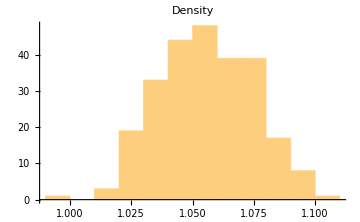
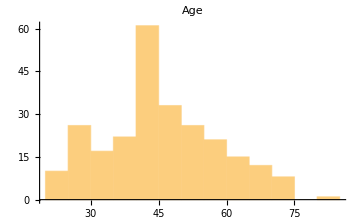
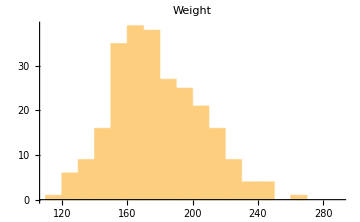
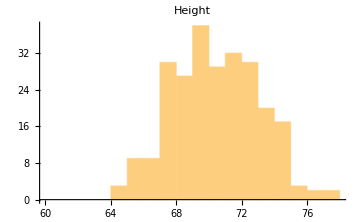
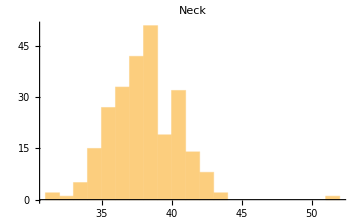
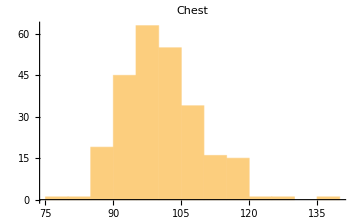
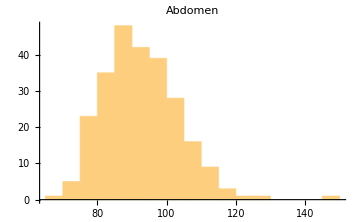
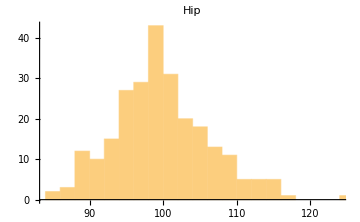

Box Plot

```mathematica
Table[ BoxWhiskerChart[bodyFatDataX[All, i] // Normal, "Outliers", PlotLabel-> predictorVariables[[i]], ImageSize->Medium], {i,1, 14, 1}]
```

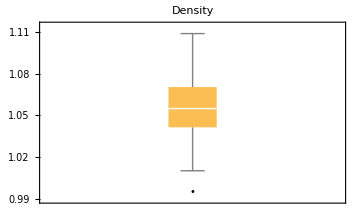
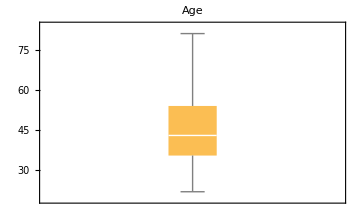
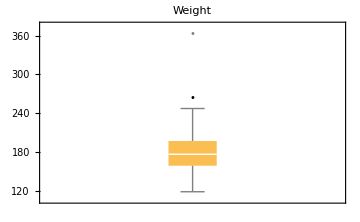
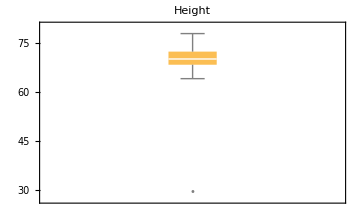
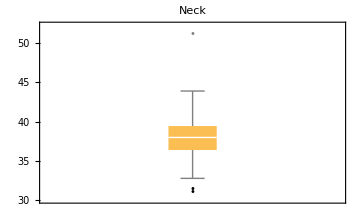
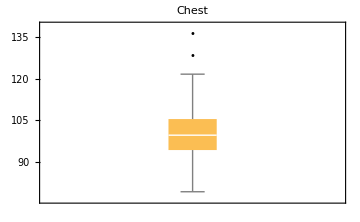
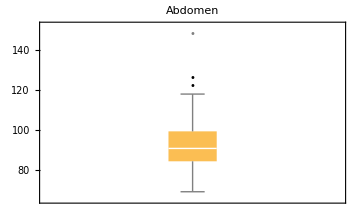
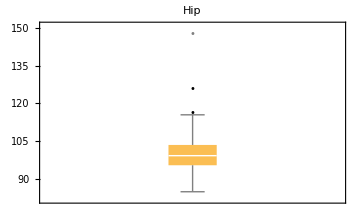

Inference: Analysing the histograms there is not much skewness in data, even though there  are  few outliers  in  variables. So by removing this  we will get much more cleaner histograms and box plots.
If these outliers are significant during modelling we have to remove it.

## Feature Selection (Correlation and Linearity)

### Linearity

We can check the linearity of the response variable with predictor variables from scatter plot.

```mathematica
linearPlots = {};
For[i=1, i< 15, i++,    AppendTo[linearPlots, ListPlot[Transpose[{bodyFatDataY[All, 1] // Normal, bodyFatDataX[All, i] // Normal}], AxesLabel->{"Body Fat",  predictorVariables[[i]]}, ImageSize-> Medium, PlotLabel->  predictorVariables[[i]]]]];
```

```mathematica
linearPlots(* Displaying Plots *)
```

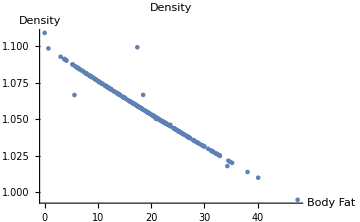
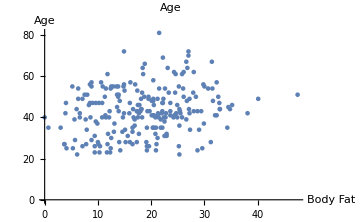
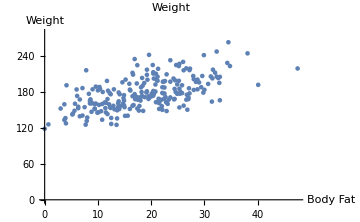
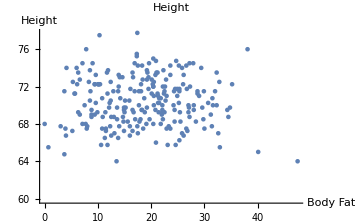
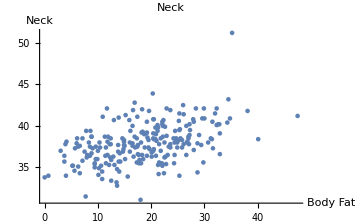
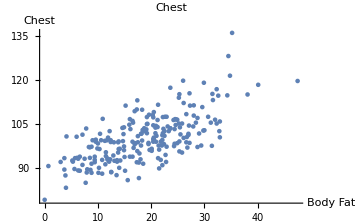
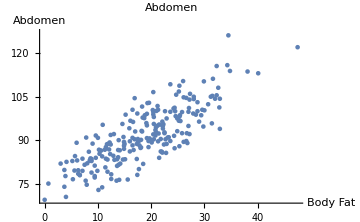
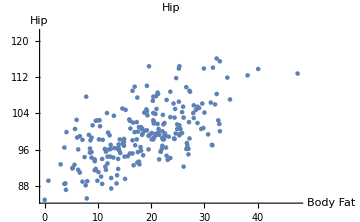

```mathematica
Needs["StatisticalPlots`"];
```

```mathematica
PairwiseScatterPlot[Values[bodyFatData] //  Normal, DataLabels->{"Density", "bodyfat", "Age", "Weight", "Height", "Neck", "Chest", "Abdomen", "Hip", "Thigh", "Knee", "Ankle", "Biceps", "Forearm", "Wrist"}, ImageSize-> {1000}]
```

-Graphics-

Inference

Relation of body fat with:

Density:  Strong linear Relation
Age:  Weak linear Relation 
Weight: Moderate linear Relation
Neck:  Moderate linear Relation 
Chest: Moderate linear Relation
Abdomen: Moderate linear Relation 
Hip: Moderate linear Relation
Height:  Weak linear Relation (Negative)
Thigh:  Moderate linear Relation
Knee:  Moderate linear Relation
Ankle:  Weak linear Relation
Biceps:  Moderate linear Relation
Forearm:  Moderate linear Relation 
Wrist:  Weak linear Relation

### Correlation

Correlation is a statistical technique that can show whether and how strongly pairs of variables are related. Here we have to find correlation between the response variable (body fat) and the predictor variables.

```mathematica
labels = {"Density", "bodyfat", "Age", "Weight", "Height", "Neck", "Chest", "Abdomen", "Hip", "Thigh", "Knee", "Ankle", "Biceps", "Forearm", "Wrist"};
```

```mathematica
corMat = Correlation[Normal[Values[bodyFatData]]];
```

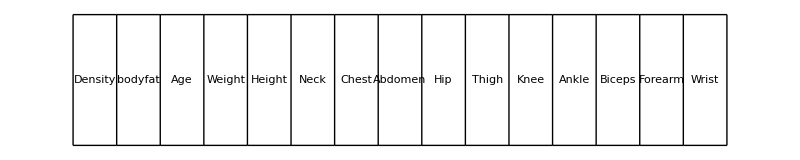
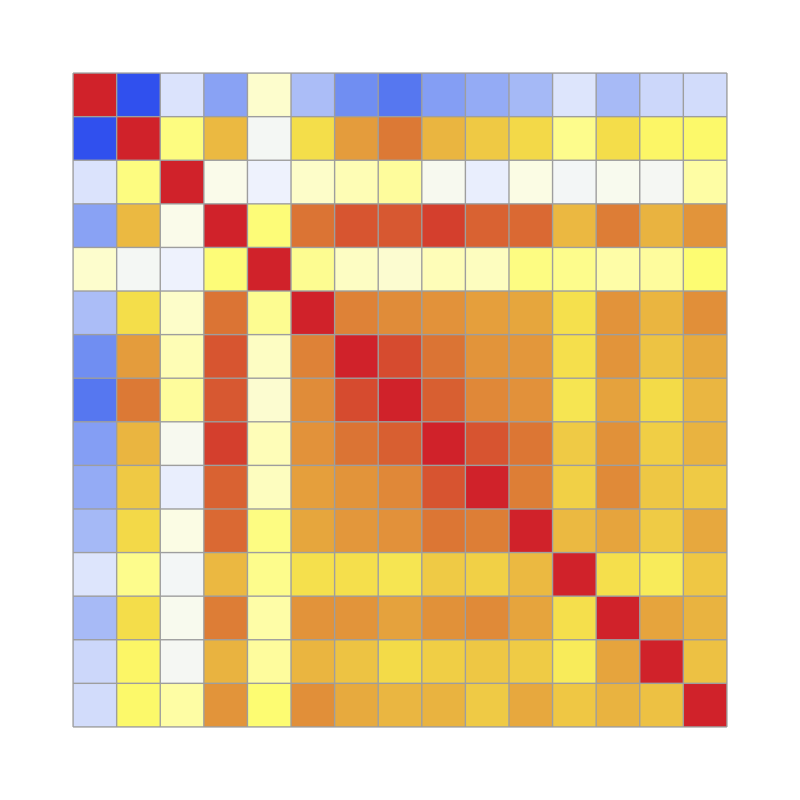
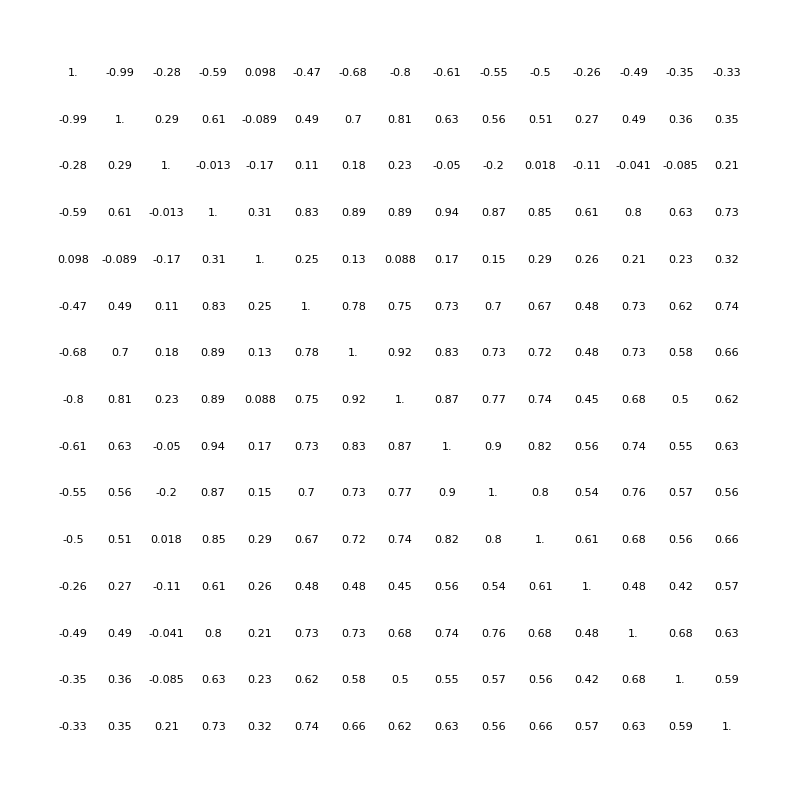
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
Column[{GraphicsRow[labels,ImageSize->800,Frame->All],Row[{GraphicsColumn[labels,ImageSize->{55,800},
     Frame->All],Overlay[{ArrayPlot[corMat,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),
Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->{800,800},ColorFunctionScaling->False],
   GraphicsGrid[Map[NumberForm[#,2]&,corMat,{2}],ImageSize->{800,800}]}]}]},Alignment->Right,Spacings->0]
```

Inference
Body fat is strongly to weekly related to:

Age: Weak Positive Relation (0.22)
Weight: Moderate Positive Relation(0.6)
Neck:  Weak Positive Relation (0.46)
Chest: Moderate Positive Relation(0.6)
Abdomen: Strong Positive Relation (0.79)
Hip: Moderate Positive Relation(0.61)
Height: Weak Negative Relation (-0.08)
Thigh: Moderate Positive Relation(0.58)
Knee: Moderate Positive Relation(0.49)
Ankle: Weak Positive Relation (0.27)
Biceps: Moderate Positive Relation (0.49)
Forearm: Weak Positive Relation (0.35)
Wrist: Weak Positive Relation (0.30)

From the correlation data we can clearly see that Density, Abdomen have strong relation with the response variable Body Fat. The variable height  is not contributing much to the target variable. So, we can remove height from model.
So, selected variables after correlation check are: Density, Weight, Neck, Chest, Abdomen, Hip, Thigh, Knee, Biceps, Forearm, Wrist.

Multicollinearity: It refers to predictor variables  that are correlated with other predictor variables.  It occurs when we have  multiple features  that are correlated not just to your response variable, but also to each other. 

Problems of multicollinearity are:
             - The coefficient estimates can swing wildly based on which other independent variables are in the model. 
             - The coefficients become very sensitive to small changes in the model.
             - Multicollinearity reduces the precision of the estimate coefficients, which weakens the statistical power of your regression model. 
             
So, to get a good model we have to remove the correlated predictor variables.

Checking multicollinearity

1. Density has no strong relation with other predictor variables

2. Chest and Hip  are strongly correlated with Abdomen, hence we can avoid these two variables in our model.

3. Thigh , Knee, Biceps and Neck  are strongly correlated with Weight, hence we can avoid including these in our model. (Other correlated ones are already removed)

4. Forearm has no strong relation with other predictor variables

5. Age,  Wrist,and Ankle doesn’t has no strong relation with other predictor variables.

So, Considering linearity and correlation, the selected variables = [ Density, Age,  weight,  Abdomen, Forearm, Wrist,  Ankle]

## Modelling - Multiple Linear Regression

Multiple linear regression is used to explain the relationship between the continuous dependent variable and two or more independent variables.  The independent variables can be continuous or categorical.

Model
                                                   Yi = B0 + B1Xi1 +  B2Xi2 + B3Xi3 + BpXip + E
                               Where,
                                                               Bo, ...Bp   -- Model Parameters
                                                               Xi1, ... Xip -- Explanatory(Feature) variables, i = 1,.,n
                                                               E -- Error
                                                               Yi -- Predicted output

In matrix form it can be represented as, 
                                                  [Vector Y] = [Feature Matrix (X)] [Parameter Vector] + [Error Vector]
                                                            n x 1                                 n x p                                            p x 1                                         n x 1
                                                           
Least Square Estimation: The least squares method is a regression analysis that finds the line of best fit for a dataset, which gives a visual demonstration of the relationship between the data points. Each point of data is representative of the relationship between a known independent variable and an unknown dependent variable. It will try to fit a line which have minimal error from each data point.

Least square estimation for the multiple linear regression for the parameters is given by the formula;
                                                                                  β = (X^T X)^-1 X^T Y

Creating feature matrix:

```mathematica
( *  Density, Age,  Weight,  Abdomen, Forearm, Wrist,  Ankle *)
```

```mathematica
X = Transpose[{ConstantArray[1,Length[bodyFatDataX[All, 1]]],  bodyFatDataX[All, "Density"] // Normal, bodyFatDataX[All, "Age"] // Normal, 
bodyFatDataX[All, "Weight"] // Normal, bodyFatDataX[All, "Abdomen"] // Normal, bodyFatDataX[All, "Forearm"] // Normal ,
bodyFatDataX[All, "Wrist"] // Normal,  bodyFatDataX[All, "Ankle"] // Normal}];
```

Output vector:

```mathematica
Y = bodyFatDataY[All, 1] // Normal;
```

### Calculating the coefficients

1.  Applying  formula (X^T X)^-1 X^T Y

```mathematica
betaCoefficents = Inverse[(Transpose[X].X)].(Transpose[X].Y) (* Beta values *)
```

{448.261,-409.706,0.0143101,0.00786871,0.0370165,0.0136284,-0.0352327,-0.0804701}

2. Using Mathematica built in method (LinearModelFit)

```mathematica
model1 = LinearModelFit[{X, Y}]
```

FittedModel[448.261 #1-409.706 #2+0.0143101 #3+0.00786871 #4+0.0370165 #5+0.0136284 #6-0.0352327 #7-0.0804701 #8]

```mathematica
model1["BestFitParameters"]
```

{448.284,-409.764,0.014459,0.00784215,0.0369239,0.0135253,-0.0314076,-0.0813976}

Inference: Matrix multiplication method and built in method produced exactly same results.

ANOVA Test

```mathematica
( *  Density, Age,  Weight,  Abdomen, Forearm, Wrist,  Ankle *)
```

```mathematica
model["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
#2 | 1 | 16941.2 | 16941.2 | 10521.9 | 1.93899×10^-201
#3 | 1 | 5.56941 | 5.56941 | 3.45908 | 0.0641188
#4 | 1 | 24.072 | 24.072 | 14.9508 | 0.000141855
#5 | 1 | 4.38144 | 4.38144 | 2.72125 | 0.100318
#6 | 1 | 0.0557765 | 0.0557765 | 0.034642 | 0.852504
#7 | 1 | 0.441248 | 0.441248 | 0.274053 | 0.601105
#8 | 1 | 2.61237 | 2.61237 | 1.6225 | 0.203965
Error | 242 | 389.64 | 1.61008 |  | 
Total | 249 | 17368. |  |  |

Since, the probability of becoming coefficient 0 is large for Forearm, Wrist & Ankle. So we can avoid those feature variables from our model.

So, Final model will be left with Density, Age, Weight, Abdomen

Re-Running Model

```mathematica
X = Transpose[{ConstantArray[1,Length[bodyFatDataX[All, 1]]],  bodyFatDataX[All, "Density"] // Normal, bodyFatDataX[All, "Age"] // Normal, 
bodyFatDataX[All, "Weight"] // Normal, bodyFatDataX[All, "Abdomen"] // Normal}];
```

```mathematica
model = LinearModelFit[{X, Y}]
```

FittedModel[446.716 #1-409.869 #2+0.0132465 #3+0.00268492 #4+0.0432823 #5]

```mathematica
model["BestFitParameters"]
```

{446.716,-409.869,0.0132465,0.00268492,0.0432823}

```mathematica
betaCoefficents = Inverse[(Transpose[X].X)].(Transpose[X].Y)
```

{446.716,-409.869,0.0132465,0.00268492,0.0432823}

Comparing Akaike information criterion (AIC)

```mathematica
model1["AIC"]  (* AIC value for model 1 *)
```

843.185

```mathematica
model["AIC"]  (* AIC value for model 2 *)
```

839.101

Model two is better since it have lower AIC value

Final Model

Yout = 446.731 - 409.894 * Density + 0.0135623 * Age + 0.00274231 * Weight + 0.0431749 * Abdomen

### Predicting Output (Yout)

```mathematica
Yout = X.betaCoefficents; (* Using the same dataset *)
```

```mathematica
Yout
```

{12.2522,6.22624,24.1999,10.7339,27.9416,21.1737,19.1274,12.5953,4.4625,11.8627,7.2017,8.39476,20.8412,21.5377,22.1865,20.8119,28.4575,22.8806,16.1547,17.2583,19.3246,15.7348,15.0551,17.2,13.5197,3.76967,7.67421,22.3451,3.50145,8.88324,11.3938,6.0403,11.5075,21.7556,32.2118,38.8575,24.4368,28.0437,36.5353,32.0881,34.5976,32.286,31.38,31.5648,7.61862,13.8741,10.4419,13.9503,13.6909,3.83684,10.647,6.75032,8.37281,6.56366,3.89274,23.1827,20.9612,28.2145,31.287,24.7716,26.6588,29.2628,30.2642,25.9132,31.8638,29.5987,21.1945,14.1757,6.69116,13.3352,24.0745,9.26515,8.94838,13.4958,12.2311,14.3362,9.01142,22.6016,22.1004,19.4474,30.547,26.2454,19.199,26.7226,27.0676,25.3571,15.5029,23.0397,8.83184,14.3225,20.7825,18.4377,8.98906,24.7236,9.57514,1.98332,10.3421,11.7117,17.835,22.4085,21.5753,20.5007,19.9703,22.3476,25.3089,17.7649,19.9992,19.1936,17.43,21.2938,19.7767,27.8203,22.0371,21.147,26.3088,16.6767,20.2029,14.3768,25.2522,18.124,27.6863,25.1991,14.701,16.0575,13.9081,17.8337,26.6995,17.1796,21.0119,15.0957,18.258,22.4122,23.8928,25.6481,23.788,27.0124,21.4755,28.8294,21.9623,21.2644,24.7312,18.529,23.1249,9.14479,10.5225,13.958,19.3989,28.8413,5.08506,25.3689,9.32995,20.1816,9.55857,16.367,21.0373,17.0663,30.4196,10.2878,12.1756,22.0333,9.52859,15.0668,13.4475,14.9785,27.417,19.5056,21.5571,20.8043,35.6062,16.6934,3.31724,0.533765,20.4116,17.1232,25.5658,9.88977,13.1266,29.8762,22.2474,17.788,26.6402,-3.86069,11.6897,12.3007,17.7324,8.95158,24.1996,20.8398,20.8387,24.4647,11.4888,37.2221,16.3591,24.9233,22.3125,25.1128,21.4021,17.9005,6.84864,22.6958,12.6423,21.6714,28.4614,6.75924,34.6429,17.0909,31.7936,32.0117,9.94753,11.126,7.36857,27.4143,19.5266,19.1178,19.6,45.4246,13.6835,7.84057,24.7225,15.322,12.8239,26.4489,11.9554,5.67284,11.9581,12.5868,15.3345,25.2345,15.4671,17.3631,11.2701,16.874,15.839,26.4827,25.653,19.1285,25.0798,28.1086,12.8269,29.5622,17.0355,34.9815,30.6733,32.6893,29.1341,15.5107,30.5645,11.5207,33.1984,29.7493,26.3643,31.852}

## Diagnosis

### SSE (Sum Of Square Error)

SSE measures the total deviation of the response values from the predicted to the output values. It is also called the summed square of residuals and is usually labelled as SSE. A value closer to 0 indicates that the model has a smaller random error component, and that the fit will be more useful for the prediction.

                                                                               SSE = ∑_(i=1)^N (Yi - Yihat)^2

```mathematica
SSE = Apply[Plus,(Yout - Y) ^ 2]
```

389.779

### MSE (Mean Square Error)

it standard error and the standard error of the regression. It is an estimate of the standard deviation of the random component in the data, and is defined 

                                                                               MSE = SSE/ N - P

                                                                                           Where,  N - Number of observation
                                                                                                            P - Number of features
Root Mean Square Error (RMSE) = MSE^(1/2)

Just like SSE, an MSE value closer to 0 indicates a fit which is more useful for prediction.

```mathematica
MSE=SSE/(252-6)
```

1.59707

```mathematica
RMSE = MSE^(1/2)
```

1.26375

### R^2

R-squared is a statistical measure of how close the data are to the fitted regression line. It is also known as the coefficient of determination, or the coefficient of multiple determination for multiple regression. It is always between 0 - 100%.

                                                                               R^2 = SSR/(SSR + SSE)

                                                                                            Where,  SSR -  ∑_(i=1)^N (Yihat - Mean Y)^2
                                                                                                             SSE - Sum of Square Error

```mathematica
MeanY = bodyFatDataY[Mean, 1];
```

```mathematica
SSR=Apply[Plus,(Yout-MeanY)^2];
R2=SSR/(SSR+SSE)
```

0.977651

```mathematica
model["RSquared"]  (*Using LinearModelFit*)
```

0.977651

```mathematica
model["AdjustedRSquared"] (* For multiple linear regression*)
```

0.977289

It means about 97 % of output body-fat variation is explained by the feature variables selected.

### Model Plots (Using LinearModelFit)

Residual Plot

A residual plot is a graph that shows the residuals on the vertical axis and the independent variable on the horizontal axis. If the points in a residual plot are randomly dispersed around the horizontal axis, a linear regression model is appropriate for the data

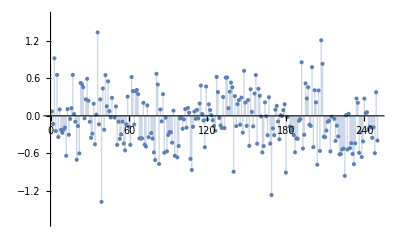

```mathematica
ListPlot[model["FitResiduals"], Filling->Axis]
```

Residual plot pattern is random.

Cooks Distances

Cook’s distance measures the effect of deleting a given observation

```mathematica
cd = model["CookDistances"];
```

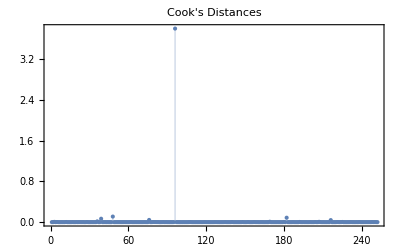

```mathematica
ListPlot[cd,Filling->0,Frame->True,AxesOrigin->{0,0},PlotRange->All,PlotLabel->"Cook's Distances"]
```

One observation is showing higher value, result will be improved if we delete the specified row.

Quantile Plot

If the points in quantile plot is following a roughly straight line then the model is performing good.

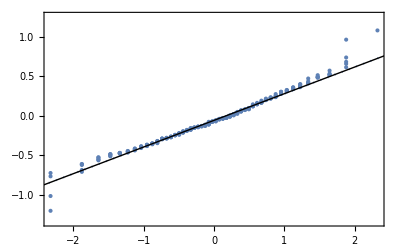

```mathematica
QuantilePlot[model["StudentizedResiduals"],Table[InverseCDF[NormalDistribution[],q],{q,1/100,99/100,1/50}]]
```

Coefficient of variation

The coefficient of variation (CV) is the ratio of the standard deviation to the mean. The higher the coefficient of variation, the greater the level of dispersion around the mean.

```mathematica
model["CoefficientOfVariation"]
```

0.0658558

Confidence interval of the parameter

```mathematica
(* Density, Age,  Weight,  Abdomen  *)
```

Confidence interval of each parameter is given by:

```mathematica
model["ParameterConfidenceIntervals"]
```

{{428.512,464.921},{-424.965,-394.772},{-0.00140202,0.0278949},{-0.0117531,0.0171229},{-0.0079486,0.0945132}}

Covariance

Covariance is a measure of how much two  variables vary together.

```mathematica
(* Density, Age,  Weight,  Abdomen  *)
```

```mathematica
model["CovarianceMatrix"]//MatrixForm
```

(85.4243 | -70.6153 | 0.00368948 | 0.028146 | -0.173732
-70.6153 | 58.7475 | -0.00307368 | -0.0221163 | 0.137194
0.00368948 | -0.00307368 | 0.0000553124 | 0.000025464 | -0.0000808571
0.028146 | -0.0221163 | 0.000025464 | 0.0000537344 | -0.000168092
-0.173732 | 0.137194 | -0.0000808571 | -0.000168092 | 0.000676552)

Prediction Vs Observed

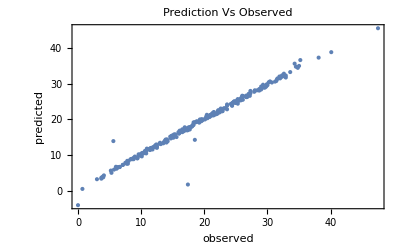

```mathematica
ListPlot[Transpose[model[{"Response","PredictedResponse"}]],FrameLabel->{"observed","predicted"},Frame->True,Axes->False, PlotLabel->"Prediction Vs Observed"]
```

```mathematica
ListPointPlot3D[{model["Response"], model["PredictedResponse"]}, PlotLabel->"Prediction Vs Observed"]
```

-Graphics3D-

## Conclusion

From the  model diagnosis its evident that model can predict the percentage body fat  in the body if we have Density (determined from underwater weighing),  Weight,  Age  &  Abdomen  with an accuracy greater than  90 percentage.